```mathematica
(* This solution uses its own stat mech equations. It does not rely on G16 to compute theromodyanmic functions. It only takes  electronic energies, moments of inertia, and vibrational frequencies from G16 *)
```

```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* constants/conversion, SI units unless specified *)
hPlank=6.626070040*10^-34; (* plank constant *)
hbar=hPlank/(2 π);
c0=299792458; (* speed of light *)
kB=1.38064852*10^-23; (* boltzmann constant *)
NA=6.022140857*10^23; (* avogadro's constant *)
Rg=kB*NA; (* gas constant *)

h2j=4.35974 10^-18;(* hartree to joule *)
amu2kg=1.660539040*10^-27; (* atomic mass to kg *)
atm2Pa=101325; (* atm to pascal *)
h2kjmol=2625.499638; (* hartree to kJ/mol *)
h2jmol=2625499.638; (* hartree to J/mol *)
MIau2kgm2=amu2kg*(5.29177×10^-11)^2; (* moment of inertia au to kg.m2 *)
```

```mathematica
(* MAIN EQUATIONS, SI units *)

(* q translational *)
Qtran[M_,T_,P_]:=((kB T)/P)((2 π M kB T)/hPlank^2)^(3/2) ;

(* q rotational *)
Qrot[MI_,T_,sig_]:=Sqrt[π]/sig((8 π^2 kB T)/hPlank^2)^(3/2)Sqrt[Apply[Times,MI]];

(* q vibrational, freq must be in sec^(-1) *)
Qvib[freq_,T_]:=Apply[Times,Exp[-(freq hPlank)/(2kB T)]]/Apply[Times,1-Exp[-(freq hPlank)/(kB T)]];

(* q electronic, make sure that energies of molecules refer to the same zero level. normally this means that the same method and basis sets are used *)
Qelec[Egs_,Wgs_,T_]:=Wgs Exp[-Egs/(kB T)]

(* Internal energy *)
VibE[x_,T_]=hPlank(x/2+x/(Exp[hPlank x/(kB T)]-1));
TranE[T_]=kB T 3/2;
RotE[T_]=kB T 3/2;
(* Many-atom molecule *)
En[freq_,Egs_,T_]:=Egs+RotE[T]+TranE[T]+ Total[VibE[#,T]&/@freq];
(* Single atom/ion does not have rotations and vibrations *)
EnAtom[Egs_,T_]:=Egs+TranE[T];

(* Enthalpy *)
H[freq_,Egs_,T_]:=En[freq,Egs,T]+kB T
HAtom[Egs_,T_]:=EnAtom[Egs,T]+kB T

(* Helmholtz free energy *)
A[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs]+Log[Qrot[MI,T,sig]]+Log[Qvib[freq,T]])+Egs
AAtom[M_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs])+Egs

(* Gibbs free energy *)
G[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=A[M,MI,sig,freq,Egs,Wgs,T,P]+kB T
GAtom[M_,Egs_,Wgs_,T_,P_]:=AAtom[M,Egs,Wgs,T,P]+kB T
```

```mathematica
(* Molecular characteristic, can be found in G16 output files *)

Print["Molecule A"];
MA =120.05751*amu2kg; (* molecular mass *)
MIA={491.06029,1488.22724,1968.09311}*MIau2kgm2; (* moments of inertia *)
(* to extract frequencies use bash: 

awk '/Frequencies/{printf("%.4f,%.4f,%.4f,",$3,$4,$5)}' filename.log

*)
FreqA={61.4748,153.5077,181.1399,231.0419,374.8193,413.5308,431.8786,469.5484,597.9076,603.9536,629.7564,704.3354,744.3933,778.5429,866.6412,952.1156,966.2871,993.0903,1014.5376,1015.8875,1046.3347,1049.9012,1099.5394,1118.6551,1193.1573,1212.3069,1284.7447,1345.4749,1365.5327,1393.9602,1475.6714,1480.9257,1487.3051,1533.6670,1631.6097,1651.7980,1751.4033,3051.0795,3116.6921,3166.2512,3186.3179,3196.0131,3205.8155,3216.1683,3218.8833}*c0*100;
SigmaA=1; (* rotational symmetry *)
ElectronicA=-384.925582213*h2j; (* electronic energy *)


Print["Molecule BH2"];
MBH2 =32.03745*amu2kg;
MIBH2={12.74031,74.53486,75.25956}*MIau2kgm2;
FreqBH2={406.8851,866.7245,1058.5823,1130.3892,1304.3368,1359.0564,1673.9638,1686.2768,3427.8544,3441.2439,3538.7493,3549.0595}*c0*100;
SigmaBH2=1;
ElectronicBH2=-111.877372912*h2j;


Print["Molecule A..BH2"];
MAdotBH2 =152.094965*amu2kg;
MIAdotBH2={661.38957,3901.09319,4284.62788}*MIau2kgm2;
FreqAdotBH2={20.1871,40.0810,64.8942,85.6257,115.4994,136.3181,159.0293,194.8579,218.7098,250.9675,384.1205,413.6229,428.2678,434.0549,478.8419,604.3023,606.7015,629.6497,703.2442,747.6021,779.2180,866.1455,884.1093,954.0285,970.6134,993.8991,1014.5170,1017.1183,1047.9706,1050.7324,1091.6120,1105.1607,1121.1038,1153.0810,1194.8304,1214.7726,1291.9883,1334.9737,1347.2206,1356.1881,1367.0435,1399.9266,1481.4413,1487.5898,1489.2897,1534.5127,1630.7649,1651.2941,1676.5145,1692.4664,1736.6872,3053.9272,3118.6869,3172.5453,3187.3786,3197.4968,3206.9963,3217.8523,3220.4013,3441.0290,3445.4715,3530.8850,3538.2936}*c0*100;
SigmaAdotBH2=1;
ElectronicAdotBH2=-496.812913388*h2j;


Print["Molecule A..BH2..A"];
MAdotBH2dotA =272.15248*amu2kg;
MIAdotBH2dotA={3631.03818,6892.39082,8404.99507}*MIau2kgm2;
FreqAdotBH2dotA={14.9609,32.0735,42.1778,49.9370,54.6855,67.5453,69.7536,78.7367,90.4943,109.2340,124.2587,126.1828,160.7843,165.0129,168.3114,189.1347,207.2095,238.5000,245.7297,273.0202,380.1985,383.3731,410.4180,413.2816,427.4258,432.3570,476.2535,479.2200,480.8515,600.8781,603.6305,604.5702,606.7594,629.4998,629.7125,700.4074,701.7071,747.4459,749.3722,774.8808,778.0022,862.0821,864.6009,897.8906,949.4608,950.5849,971.6030,972.3749,988.9035,991.6494,1011.2722,1013.3204,1015.3006,1015.9393,1048.8370,1050.7240,1051.2555,1051.8732,1074.4107,1103.5852,1105.5829,1121.1878,1121.5619,1153.4840,1194.4814,1194.5422,1214.7922,1215.7087,1293.1409,1295.8172,1327.5110,1347.6303,1348.5507,1367.9679,1368.8916,1382.1082,1394.8583,1400.6952,1479.0805,1480.0473,1481.7115,1482.1420,1488.2918,1488.6719,1534.8961,1535.5540,1631.5784,1632.2602,1652.1517,1652.9773,1696.7720,1705.8573,1730.5039,1735.3083,3058.1051,3059.3680,3128.5916,3131.2769,3168.7853,3177.6841,3185.7622,3188.3176,3196.1081,3198.7165,3206.1001,3208.1253,3216.8592,3218.3050,3220.7855,3221.3581,3418.7071,3424.6059,3535.1769,3545.7462}*c0*100;
SigmaAdotBH2dotA=1;
ElectronicAdotBH2dotA=-881.758711641*h2j;


Print["Molecule AAHH"];
MAAHH =242.13068*amu2kg;
MIAAHH={3196.96554,4306.50942,5933.42499}*MIau2kgm2;
FreqAAHH={30.0770,58.2449,68.1737,88.5837,111.8044,221.9282,239.7210,241.7837,253.6293,272.0035,277.4668,310.9954,327.2111,342.4626,351.1342,371.3303,384.7087,418.3039,424.5045,451.5004,464.2478,498.7361,517.4264,582.9951,595.0071,605.3111,633.4216,634.8773,650.3348,693.9419,715.7390,721.6090,773.1713,775.9046,806.7927,862.0367,862.6596,870.7145,929.8311,934.7131,943.2633,951.7082,978.6913,988.3702,1000.2540,1007.5378,1015.1398,1015.6556,1050.5088,1053.4489,1063.3125,1075.7226,1101.6264,1108.3777,1112.2459,1121.9954,1151.5235,1176.9637,1191.1770,1191.9422,1218.3151,1223.9011,1242.3204,1270.5953,1320.8378,1338.4678,1340.8080,1362.3693,1365.7049,1380.7804,1420.7763,1427.2557,1484.7121,1485.0553,1492.5663,1501.5232,1506.9350,1518.4108,1536.7178,1539.0832,1633.6317,1635.1107,1656.9458,1657.7314,3058.0988,3070.8994,3134.8468,3143.4006,3161.7308,3166.8291,3176.1063,3179.5516,3185.0827,3188.2921,3199.4274,3201.4221,3211.4950,3215.0189,3220.9942,3224.6904,3724.5551,3807.7052}*c0*100;
SigmaAAHH=1;
ElectronicAAHH=-771.061169670*h2j;


Print["Molecule B"];
MB =30.02180*amu2kg;
MIB={6.01793,46.01503,52.03296}*MIau2kgm2;
FreqB={1342.2488,1361.4080,1606.3613,1658.1557,3235.0293,3258.8340}*c0*100;
SigmaB=2;
ElectronicB=-110.647428863*h2j;


Print["Molecule AH..BH"];
MAHdotBH =152.09496*amu2kg;
MIAHdotBH={1385.68537,2240.27215,3029.47666}*MIau2kgm2;
FreqAHdotBH={24.0583,47.4965,72.2892,84.1133,108.7375,129.8236,172.0430,198.9407,226.7916,258.1902,360.6343,380.6561,428.8140,476.6077,518.1814,549.8628,569.6234,626.8356,695.3449,710.9873,738.2305,748.5411,831.4827,875.9922,942.6369,968.0994,982.5826,983.8297,999.8297,1022.6743,1041.3400,1080.1472,1114.8840,1164.5629,1183.0956,1212.6450,1265.8733,1285.9637,1332.8935,1363.0688,1400.3613,1422.7177,1450.5678,1477.5025,1486.3405,1491.3753,1497.9033,1534.3968,1579.9608,1619.0151,1662.4210,2908.5394,3000.5723,3079.6169,3131.2905,3171.6185,3176.6673,3197.3914,3204.1969,3212.6507,3472.9048,3510.2193,3651.4800}*c0*100;
SigmaAHdotBH=1;
ElectronicAHdotBH=-496.747815472*h2j;


Print["Molecule AH..BH..A"];
MAHdotBHdotA =272.15248*amu2kg;
MIAHdotBHdotA={4000.47826,6158.48322,8114.36417}*MIau2kgm2;
FreqAHdotBHdotA={19.3499,24.4618,39.8178,54.1765,65.6812,72.6658,89.3144,103.6190,121.2415,127.6908,137.5881,156.0362,165.0971,174.9433,182.7520,189.8510,205.7760,241.6541,258.5647,268.0043,356.9523,387.1170,393.2623,411.2423,415.5757,433.7707,479.8763,481.8834,512.5015,554.7840,596.3080,613.8497,627.3562,629.4918,685.6816,697.2607,730.9929,739.2339,747.3730,748.1254,753.6201,774.1354,821.1249,855.6758,871.0590,871.7580,944.4715,957.7351,970.5446,976.4988,979.0935,983.8641,991.3025,1008.8621,1015.2675,1037.2933,1041.5294,1051.1821,1056.0468,1083.9689,1100.1567,1112.7612,1120.2997,1183.0388,1193.4468,1195.8952,1210.1648,1214.0374,1285.5170,1296.3451,1300.4912,1324.3309,1346.7564,1362.4350,1368.0975,1371.5429,1401.5085,1424.1732,1473.4932,1478.4769,1487.2656,1488.4946,1494.2105,1495.8535,1506.1922,1509.7459,1534.3142,1557.9981,1584.3693,1621.1843,1629.7169,1650.3844,1685.7459,1712.0173,3015.6285,3048.0049,3071.6081,3121.6283,3129.0910,3143.9893,3158.9675,3170.2860,3176.6164,3185.2268,3197.9425,3198.6187,3208.6469,3209.7840,3216.7889,3217.2613,3228.7405,3427.4805,3448.6480,3615.0722}*c0*100;
SigmaAHdotBHdotA=1;
ElectronicAHdotBHdotA=-881.694213015*h2j;


Print["Molecule AAHH..B"];
MAAHHdotB =272.15248*amu2kg;
MIAAHHdotB={3663.08361,7007.80986,8497.76783}*MIau2kgm2;
FreqAAHHdotB={22.8466,32.3377,39.8109,55.1691,61.6716,79.4654,101.9399,110.2536,117.4488,160.8566,231.2670,233.7925,244.7980,252.3312,260.2541,280.1236,289.7498,312.7687,332.7574,359.2059,364.8587,395.1969,420.4247,427.2558,464.2896,469.1220,487.2009,514.7692,536.0409,593.4837,594.5740,632.9383,634.0654,651.2339,693.9169,718.6115,719.2773,751.7081,773.7094,779.4281,813.7204,855.7220,867.0032,869.6351,932.9158,935.7495,949.5172,953.5185,984.7806,989.2174,1004.5037,1007.6189,1015.0873,1015.5915,1049.0659,1054.5619,1068.4117,1092.2980,1099.9545,1112.5825,1118.5670,1145.8842,1154.2968,1173.2082,1190.3831,1190.7851,1216.2903,1218.2151,1228.8138,1263.0629,1331.2095,1338.4740,1339.3540,1359.8417,1361.2207,1362.5217,1383.1494,1412.5046,1419.0969,1433.4091,1484.4507,1486.1121,1495.0421,1498.6673,1513.6856,1515.6254,1535.7459,1539.0012,1595.1779,1632.2374,1633.7018,1656.0377,1658.2984,1678.6989,3065.2631,3067.6117,3144.1674,3145.3564,3153.1173,3159.3867,3177.1566,3179.1900,3186.0249,3187.8555,3200.5847,3202.5911,3218.8461,3220.2762,3221.4632,3230.8161,3270.4856,3305.3345,3493.7945,3718.9066}*c0*100;
SigmaAAHHdotB=1;
ElectronicAAHHdotB=-881.724195655*h2j;


Print["Transition state AH..BH..A"];
MTSAHdotBHdotA =272.15248*amu2kg;
MITSAHdotBHdotA={5164.44541,5647.43255,8865.25308}*MIau2kgm2;
FreqTSAHdotBHdotA={21.5188,25.6770,54.2057,62.7413,71.5964,82.7708,97.8592,115.5795,165.7377,214.7462,223.3021,234.9894,245.2619,255.7787,261.1133,268.3639,274.0937,298.4557,312.6126,363.4498,371.4836,395.3618,418.3963,428.8869,459.5593,479.5181,485.6124,529.8392,552.4157,569.4684,615.6573,626.1073,630.4823,631.6815,704.8423,709.9152,722.7036,756.2738,773.9493,782.4237,841.4907,853.1974,860.9678,924.9974,932.6076,942.0503,966.9800,978.8028,982.6357,1000.6524,1003.2875,1005.9805,1007.1174,1011.6115,1048.2585,1050.1404,1057.7670,1070.0645,1088.0063,1093.2882,1107.6934,1111.6828,1130.6464,1188.5296,1190.5620,1210.9624,1214.4373,1229.2297,1240.2365,1285.7283,1294.3842,1337.7197,1345.3087,1361.3945,1365.7802,1376.4917,1404.1283,1414.5563,1421.5722,1483.2336,1486.8224,1491.1694,1498.5523,1501.1906,1512.0509,1521.3238,1533.5351,1535.7419,1615.4443,1625.1232,1642.3623,1648.2180,1757.5429,1988.8154,3034.7413,3035.9223,3113.4837,3115.1055,3162.9985,3165.1759,3177.7261,3179.7783,3186.3781,3187.7879,3201.5288,3203.5913,3219.7142,3224.4518,3225.0828,3226.7670,3385.1921,3528.5612,3536.7230}*c0*100;
SigmaTSAHdotBHdotA=1;
ElectronicTSAHdotBHdotA=-881.659377969*h2j;
```

Molecule A

Molecule BH2

Molecule A..BH2

Molecule A..BH2..A

Molecule AAHH

Molecule B

Molecule AH..BH

Molecule AH..BH..A

Molecule AAHH..B

Transition state AH..BH..A

```mathematica
KeqT={};
KrateT={};
Do[
Do[

(* convert concetration from mol/L into SI units m^-3 *)
Csi=C0*NA*10^3;
(* compute pressure SI units *)
P0=Csi kB T0;
V0 =(kB T0)/P0;

Print[];
Print["===================="];
Style[Print["Temperature and concentration = ",T0," Kelvin, ",C0," mol/L"],Red];
Print["Ideal-gas pressure = ",P0/atm2Pa," atm"];
Print["Volume per 1 molecule in SI units = ",V0];


Print["Molecule A"];
(* calculate thermodynamic funtions at 400 K and 2 atm *)
QA=Qtran[MA,T0,P0]Qrot[MIA,T0,1]Qvib[FreqA,T0];
(* evaluate electronic partition function separately, note that this is a gigantic number, cannot be computed in G16 *)
Print["Correct electronic partition function = ",Qelec[ElectronicA,1,T0] ];
(* Gibbs free energy *)
GA=G[MA,MIA,SigmaA,FreqA,ElectronicA,1,T0,P0];
(* Compute correction to compare with G16 output *)
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GA-ElectronicA)/h2j, " hartree"];
(* Helmholtz free energy *)
AA=A[MA,MIA,SigmaA,FreqA,ElectronicA,1,T0,P0];
(* Internal energy *)
EA=En[FreqA,ElectronicA,T0];
(* Enthalpy *)
HA=H[FreqA,ElectronicA,T0];


Print["Molecule BH2"];QBH2=Qtran[MBH2,T0,P0]Qrot[MIBH2,T0,1]Qvib[FreqBH2,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicBH2,1,T0] ];
GBH2=G[MBH2,MIBH2,SigmaBH2,FreqBH2,ElectronicBH2,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GBH2-ElectronicBH2)/h2j, " hartree"];
ABH2=A[MBH2,MIBH2,SigmaBH2,FreqBH2,ElectronicBH2,1,T0,P0];
EBH2=En[FreqBH2,ElectronicBH2,T0];
HBH2=H[FreqBH2,ElectronicBH2,T0];


Print["Molecule A..BH2"];QAdotBH2 =Qtran[MAdotBH2 ,T0,P0]Qrot[MIAdotBH2 ,T0,1]Qvib[FreqAdotBH2 ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAdotBH2 ,1,T0] ];
GAdotBH2 =G[MAdotBH2 ,MIAdotBH2 ,SigmaAdotBH2 ,FreqAdotBH2 ,ElectronicAdotBH2 ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAdotBH2 -ElectronicAdotBH2 )/h2j, " hartree"];
AAdotBH2 =A[MAdotBH2 ,MIAdotBH2 ,SigmaAdotBH2 ,FreqAdotBH2 ,ElectronicAdotBH2 ,1,T0,P0];
EAdotBH2 =En[FreqAdotBH2 ,ElectronicAdotBH2 ,T0];
HAdotBH2 =H[FreqAdotBH2 ,ElectronicAdotBH2 ,T0];


Print["Molecule A..BH2..A"];QAdotBH2dotA =Qtran[MAdotBH2dotA ,T0,P0]Qrot[MIAdotBH2dotA ,T0,1]Qvib[FreqAdotBH2dotA ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAdotBH2dotA ,1,T0] ];
GAdotBH2dotA =G[MAdotBH2dotA ,MIAdotBH2dotA ,SigmaAdotBH2dotA ,FreqAdotBH2dotA ,ElectronicAdotBH2dotA ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAdotBH2dotA -ElectronicAdotBH2dotA )/h2j, " hartree"];
AAdotBH2dotA =A[MAdotBH2dotA ,MIAdotBH2dotA ,SigmaAdotBH2dotA ,FreqAdotBH2dotA ,ElectronicAdotBH2dotA ,1,T0,P0];
EAdotBH2dotA =En[FreqAdotBH2dotA ,ElectronicAdotBH2dotA ,T0];
HAdotBH2dotA =H[FreqAdotBH2dotA ,ElectronicAdotBH2dotA ,T0];


Print["Molecule AAHH"];QAAHH=Qtran[MAAHH ,T0,P0]Qrot[MIAAHH ,T0,1]Qvib[FreqAAHH ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAAHH ,1,T0] ];
GAAHH=G[MAAHH ,MIAAHH ,SigmaAAHH ,FreqAAHH ,ElectronicAAHH ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAAHH -ElectronicAAHH )/h2j, " hartree"];
AAAHH =A[MAAHH,MIAAHH,SigmaAAHH,FreqAAHH,ElectronicAAHH ,1,T0,P0];
EAAHH =En[FreqAAHH ,ElectronicAAHH ,T0];
HAAHH =H[FreqAAHH ,ElectronicAAHH ,T0];


Print["Molecule B"];QB =Qtran[MB ,T0,P0]Qrot[MIB ,T0,1]Qvib[FreqB ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicB ,1,T0] ];
GB=G[MB,MIB,SigmaB,FreqB,ElectronicB ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GB -ElectronicB )/h2j, " hartree"];
AB =A[MB ,MIB ,SigmaB ,FreqB ,ElectronicB,1,T0,P0];
EB =En[FreqB ,ElectronicB ,T0];
HB =H[FreqB ,ElectronicB ,T0];


Print["Molecule AH..BH"];QAHdotBH =Qtran[MAHdotBH ,T0,P0]Qrot[MIAHdotBH ,T0,1]Qvib[FreqAHdotBH ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAHdotBH ,1,T0] ];
GAHdotBH=G[MAHdotBH ,MIAHdotBH ,SigmaAHdotBH ,FreqAHdotBH ,ElectronicAHdotBH ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAHdotBH -ElectronicAHdotBH )/h2j, " hartree"];
AAHdotBH =A[MAHdotBH,MIAHdotBH ,SigmaAHdotBH,FreqAHdotBH,ElectronicAHdotBH ,1,T0,P0];
EAHdotBH =En[FreqAHdotBH ,ElectronicAHdotBH ,T0];
HAHdotBH =H[FreqAHdotBH ,ElectronicAHdotBH ,T0];


Print["Molecule AAHH..B"];QAAHHdotB =Qtran[MAAHHdotB ,T0,P0]Qrot[MIAAHHdotB ,T0,1]Qvib[FreqAAHHdotB ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAAHHdotB ,1,T0] ];
GAAHHdotB=G[MAAHHdotB ,MIAAHHdotB,SigmaAAHHdotB ,FreqAAHHdotB ,ElectronicAAHHdotB ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAAHHdotB -ElectronicAAHHdotB )/h2j, " hartree"];
AAAHHdotB =A[MAAHHdotB ,MIAAHHdotB ,SigmaAAHHdotB ,FreqAAHHdotB ,ElectronicAAHHdotB ,1,T0,P0];
EAAHHdotB =En[FreqAAHHdotB,ElectronicAAHHdotB ,T0];
HAAHHdotB =H[FreqAAHHdotB ,ElectronicAAHHdotB ,T0];


Print["Molecule AH..BH..A"];QAHdotBHdotA =Qtran[MAHdotBHdotA ,T0,P0]Qrot[MIAHdotBHdotA ,T0,1]Qvib[FreqAHdotBHdotA ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicAHdotBHdotA ,1,T0] ];
GAHdotBHdotA =G[MAHdotBHdotA ,MIAHdotBHdotA ,SigmaAHdotBHdotA ,FreqAHdotBHdotA ,ElectronicAHdotBHdotA ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GAHdotBHdotA -ElectronicAHdotBHdotA )/h2j, " hartree"];
AAHdotBHdotA =A[MAHdotBHdotA ,MIAHdotBHdotA ,SigmaAHdotBHdotA ,FreqAHdotBHdotA ,ElectronicAHdotBHdotA ,1,T0,P0];
EAHdotBHdotA =En[FreqAHdotBHdotA ,ElectronicAHdotBHdotA ,T0];
HAHdotBHdotA =H[FreqAHdotBHdotA ,ElectronicAHdotBHdotA ,T0];


Print["Transition state AH..BH..A"];QTSAHdotBHdotA =Qtran[MTSAHdotBHdotA ,T0,P0]Qrot[MITSAHdotBHdotA ,T0,1]Qvib[FreqTSAHdotBHdotA ,T0];
Print["Correct electronic partition function = ",Qelec[ElectronicTSAHdotBHdotA ,1,T0] ];
GTSAHdotBHdotA =G[MTSAHdotBHdotA ,MITSAHdotBHdotA ,SigmaTSAHdotBHdotA ,FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,1,T0,P0];
Print["Sanity check. Compare to G16 output. G thermal correction = ",(GTSAHdotBHdotA -ElectronicTSAHdotBHdotA )/h2j, " hartree"];
ATSAHdotBHdotA =A[MTSAHdotBHdotA ,MITSAHdotBHdotA ,SigmaTSAHdotBHdotA ,FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,1,T0,P0];
ETSAHdotBHdotA =En[FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,T0];
HTSAHdotBHdotA =H[FreqTSAHdotBHdotA ,ElectronicTSAHdotBHdotA ,T0];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 1, path 1 (R1P1): A + BH2 <-> A..BH2"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAdotBH2-ElectronicA - ElectronicBH2)*NA;
(* Internal E, J/mol *)
DeltaE=(EAdotBH2-EA-EBH2)*NA;
(* Enthalpy change *)
DeltaH=(HAdotBH2-HA-HBH2)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAdotBH2-GA-GBH2)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAdotBH2-AA-ABH2)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = QAdotBH2/(QA QBH2)Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR1P1 = (QAdotBH2/V0)/((QA/V0)( QBH2/V0))Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR1P1," m^3 or ",KeqR1P1*10^3*NA," L * mol^-1"];


(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 2, path 1 (R2P1): A..BH2 <-> AH..BH"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAHdotBH-ElectronicAdotBH2)*NA;
(* Internal E, J/mol *)
DeltaE=(EAHdotBH-EAdotBH2)*NA;
(* Enthalpy change *)
DeltaH=(HAHdotBH-HAdotBH2)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAHdotBH-GAdotBH2)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAHdotBH-AAdotBH2)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = QAHdotBH/QAdotBH2 Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR2P1 = (QAHdotBH/V0)/(QAdotBH2/V0)Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR2P1];


(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 3, path 1 (R3P1): AH..BH + A <-> AH..BH..A"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAHdotBHdotA-ElectronicAHdotBH-ElectronicA)*NA;
(* Internal E, J/mol *)
DeltaE=(EAHdotBHdotA-EAHdotBH-EA)*NA;
(* Enthalpy change *)
DeltaH=(HAHdotBHdotA-HAHdotBH-HA)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAHdotBHdotA-GAHdotBH-GA)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAHdotBHdotA-AAHdotBH-AA)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = QAHdotBHdotA/(QA QAHdotBH)Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR3P1 = (QAHdotBHdotA/V0)/((QA/V0) (QAHdotBH/V0))Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR3P1," m^3 or ",KeqR3P1*10^3*NA," L * mol^-1"];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 4, path 1 (R4P1): AH..BH..A <-> AAHH..B"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAAHHdotB-ElectronicAHdotBHdotA)*NA;
(* Internal E, J/mol *)
DeltaE=(EAAHHdotB-EAHdotBHdotA)*NA;
(* Enthalpy change *)
DeltaH=(HAAHHdotB-HAHdotBHdotA)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAAHHdotB-GAHdotBHdotA)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAAHHdotB-AAHdotBHdotA)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = QAAHHdotB/QAHdotBHdotA Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR4P1 = (QAAHHdotB/V0)/(QAHdotBHdotA/V0)Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR4P1];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 5, path 1 (R5P1): AAHH..B <-> AAHH + B"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAAHH +ElectronicB-ElectronicAAHHdotB)*NA;
(* Internal E, J/mol *)
DeltaE=(EAAHH +EB-EAAHHdotB)*NA;
(* Enthalpy change *)
DeltaH=(HAAHH +HB-HAAHHdotB)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAAHH +GB-GAAHHdotB)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAAHH +AB-AAAHHdotB)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = (QAAHH QB)/QAAHHdotB Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR5P1 = ((QAAHH/V0) (QB/V0))/(QAAHHdotB/V0)Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR5P1," m^-3 or ",KeqR5P1/(10^3*NA)," L * mol^-1"];





(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 1, path 2 (R1P2): 2A + BH2 <-> A..BH2..A"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAdotBH2dotA-2*ElectronicA - ElectronicBH2)*NA;
(* Internal E, J/mol *)
DeltaE=(EAdotBH2dotA-2*EA-EBH2)*NA;
(* Enthalpy change *)
DeltaH=(HAdotBH2dotA-2*HA-HBH2)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAdotBH2dotA-2*GA-GBH2)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAdotBH2dotA-2*AA-ABH2)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = QAdotBH2dotA/(QA QBH2 QA)Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR1P2 = (QAdotBH2dotA/V0)/((QA/V0)^2( QBH2/V0))Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR1P2," m^6 or ",KeqR1P2*(10^3*NA)^2," L^2* mol^-2"];


(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 2, path 2 (R2P2): A..BH2..A <-> AH..BH..A"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicAHdotBHdotA-ElectronicAdotBH2dotA)*NA;
(* Internal E, J/mol *)
DeltaE=(EAHdotBHdotA-EAdotBH2dotA)*NA;
(* Enthalpy change *)
DeltaH=(HAHdotBHdotA-HAdotBH2dotA)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GAHdotBHdotA-GAdotBH2dotA)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AAHdotBHdotA-AAdotBH2dotA)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta E(intr) = ",DeltaE];
Print["Delta H = ",DeltaH];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = QAHdotBHdotA/QAdotBH2dotA Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR2P2 = (QAHdotBHdotA/V0)/(QAdotBH2dotA/V0)Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR2P2];


Print[];
Print["Reaction 3, path 2 (R2P2): see Reaction 4, path 1"];

Print[];
Print["Reaction 4, path 2 (R2P2): see Reaction 5, path 1"];


(*
(* now use gibbs free energy to get the same constant *)
(* this expression is valid only for reactions with Delta N = 0 *)
Keq2=Exp[-DeltaG/(NA kB T0)];

Print["Use reaction free energy. Equilibrium constant = ",Keq2];

KeqT=Append[KeqT,{T0,Keq2}];
*)



(* Rate constant *)

Print[];
Print["Transition state for Reaction 4, path 1 (R4P1): AH..BH..A <-> AAHH..B"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicTSAHdotBHdotA-ElectronicAHdotBHdotA)*NA;
(* Internal E, J/mol *)
DeltaE=(ETSAHdotBHdotA-EAHdotBHdotA)*NA;
(* Enthalpy change *)
DeltaH=(HTSAHdotBHdotA-HAHdotBHdotA)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GTSAHdotBHdotA-GAHdotBHdotA)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(ATSAHdotBHdotA-AAHdotBHdotA)*NA;

Print["Energy units are J/mol."];Print["Act. Delta E(elec) = ",DeltaEelectronic];
Print["Act. Delta E(intr) = ",DeltaE];
Print["Act. Delta H = ",DeltaH];
Print["Act. Delta A = ",DeltaA];
Print["Act. Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Act. Delta S = ",(DeltaH-DeltaG)/T0];

KrateR4P1 =(kB T0)/hPlank Exp[-(ElectronicTSAHdotBHdotA-ElectronicAHdotBHdotA)/(kB T0)]((QTSAHdotBHdotA/V0)/(QAHdotBHdotA/V0));
Print["Use partition functions. Rate constant = ",KrateR4P1," s^(-1)"];
KrateR4P1 =(kB T0)/hPlank Exp[-(GTSAHdotBHdotA-GAHdotBHdotA)/(kB T0)];
Print["Use activation free energy. Rate constant = ",KrateR4P1," s^(-1)"];

(* save current temperature data into a list: 1/RT vs. Log K_rate *)
KrateT=Append[KrateT,    {1/(kB NA T0),Log[KrateR4P1]}    ];


Print[];
Print["Done with temperature/concentration: ",T0, ", ",C0];
Print["===================="];

,{T0,298.15,298.15,10}]
,{C0,1,1,1}]
 (* Temperature (Kelvin) and concetration (mol/L) *)
```

====================

Temperature and concentration = 298.15 Kelvin, 1 mol/L

Ideal-gas pressure = 24.4654 atm

Volume per 1 molecule in SI units = 1.66054×10^-27

Molecule A

Correct electronic partition function = 1.513649408×10^177053

Sanity check. Compare to G16 output. G thermal correction = 0.108563 hartree

Molecule BH2

Correct electronic partition function = 8.569162403×10^51459

Sanity check. Compare to G16 output. G thermal correction = 0.033789 hartree

Molecule A..BH2

Correct electronic partition function = 4.936725676×10^228517

Sanity check. Compare to G16 output. G thermal correction = 0.155883 hartree

Molecule A..BH2..A

Correct electronic partition function = 1.48655707×10^405580

Sanity check. Compare to G16 output. G thermal correction = 0.282923 hartree

Molecule AAHH

Correct electronic partition function = 8.37323686×10^354662

Sanity check. Compare to G16 output. G thermal correction = 0.264489 hartree

Molecule B

Correct electronic partition function = 1.580874246×10^50894

Sanity check. Compare to G16 output. G thermal correction = 0.010442 hartree

Molecule AH..BH

Correct electronic partition function = 5.630234189×10^228487

Sanity check. Compare to G16 output. G thermal correction = 0.152024 hartree

Molecule AAHH..B

Correct electronic partition function = 1.97677284×10^405564

Sanity check. Compare to G16 output. G thermal correction = 0.288275 hartree

Molecule AH..BH..A

Correct electronic partition function = 3.19832693×10^405550

Sanity check. Compare to G16 output. G thermal correction = 0.280808 hartree

Transition state AH..BH..A

Correct electronic partition function = 3.03347811×10^405534

Sanity check. Compare to G16 output. G thermal correction = 0.282435 hartree

Reaction 1, path 1 (R1P1): A + BH2 <-> A..BH2

Energy units are J/mol.

Delta E(elec) = -26145.4

Delta E(intr) = -17052.8

Delta H = -19531.7

Delta A = 11857.6

Delta G = 9378.6

Entropy units are J/mol/K.

Delta S = -96.9657

T- and p-dependent number constant = 0.0227478

Use partition functions. Equilibrium constant = 3.77736×10^-29 m^3 or 0.0227478 L * mol^-1

Reaction 2, path 1 (R2P1): A..BH2 <-> AH..BH

Energy units are J/mol.

Delta E(elec) = 170914.

Delta E(intr) = 160071.

Delta H = 160071.

Delta A = 160783.

Delta G = 160783.

Entropy units are J/mol/K.

Delta S = -2.38763

T- and p-dependent number constant = 6.79278×10^-29

Use partition functions. Equilibrium constant = 6.79278×10^-29

Reaction 3, path 1 (R3P1): AH..BH + A <-> AH..BH..A

Energy units are J/mol.

Delta E(elec) = -54650.6

Delta E(intr) = -44648.2

Delta H = -47127.1

Delta A = 916.588

Delta G = -1562.37

Entropy units are J/mol/K.

Delta S = -152.825

T- and p-dependent number constant = 1.87808

Use partition functions. Equilibrium constant = 3.11863×10^-27 m^3 or 1.87808 L * mol^-1

Reaction 4, path 1 (R4P1): AH..BH..A <-> AAHH..B

Energy units are J/mol.

Delta E(elec) = -78719.3

Delta E(intr) = -70624.8

Delta H = -70624.8

Delta A = -59113.8

Delta G = -59113.8

Entropy units are J/mol/K.

Delta S = -38.608

T- and p-dependent number constant = 2.27137×10^10

Use partition functions. Equilibrium constant = 2.27137×10^10

Reaction 5, path 1 (R5P1): AAHH..B <-> AAHH + B

Energy units are J/mol.

Delta E(elec) = 40950.2

Delta E(intr) = 31811.8

Delta H = 34290.7

Delta A = 3436.09

Delta G = 5915.05

Entropy units are J/mol/K.

Delta S = 95.1725

T- and p-dependent number constant = 0.183975

Use partition functions. Equilibrium constant = 1.10792×10^26 m^-3 or 0.183975 L * mol^-1

Reaction 1, path 2 (R1P2): 2A + BH2 <-> A..BH2..A

Energy units are J/mol.

Delta E(elec) = -79222.5

Delta E(intr) = -61617.1

Delta H = -66575.

Delta A = 9769.67

Delta G = 4811.76

Entropy units are J/mol/K.

Delta S = -239.432

T- and p-dependent number constant = 0.143554

Use partition functions. Equilibrium constant = 3.95836×10^-55 m^6 or 0.143554 L^2* mol^-2

Reaction 2, path 2 (R2P2): A..BH2..A <-> AH..BH..A

Energy units are J/mol.

Delta E(elec) = 169341.

Delta E(intr) = 159987.

Delta H = 159987.

Delta A = 163787.

Delta G = 163787.

Entropy units are J/mol/K.

Delta S = -12.7459

T- and p-dependent number constant = 2.02156×10^-29

Use partition functions. Equilibrium constant = 2.02156×10^-29

Reaction 3, path 2 (R2P2): see Reaction 4, path 1

Reaction 4, path 2 (R2P2): see Reaction 5, path 1

Transition state for Reaction 4, path 1 (R4P1): AH..BH..A <-> AAHH..B

Energy units are J/mol.

Act. Delta E(elec) = 91459.3

Act. Delta E(intr) = 82385.4

Act. Delta H = 82385.4

Act. Delta A = 95731.3

Act. Delta G = 95731.3

Entropy units are J/mol/K.

Act. Delta S = -44.7624

Use partition functions. Rate constant = 0.000105162 s^(-1)

Use activation free energy. Rate constant = 0.000105162 s^(-1)

Done with temperature/concentration: 298.15, 1

====================

```mathematica
SolutionR1P1=Solve[Cx/(C0-Cx)^2==KeqR1P1*(10^3*NA),Cx]
SolutionR1P2=Solve[Cx/(C0-Cx)^3==KeqR1P2*(10^3*NA)^2,Cx]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Cx→1.00052×10^-7 (2.19687×10^8+9.9948×10^6 C0-14821.8 √(2.19687×10^8+1.99896×10^7 C0))},{Cx→1.00052×10^-7 (2.19687×10^8+9.9948×10^6 C0+14821.8 √(2.19687×10^8+1.99896×10^7 C0))}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Cx→C0+(3.11751×10^6-5.39969×10^6 ⅈ)/((-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3))-(1.86206×10^-7+3.22519×10^-7 ⅈ) (-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3)},{Cx→C0+(3.11751×10^6+5.39969×10^6 ⅈ)/((-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3))-(1.86206×10^-7-3.22519×10^-7 ⅈ) (-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3)},{Cx→C0-(6.23502×10^6)/((-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3))+3.72412×10^-7 (-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3)}}

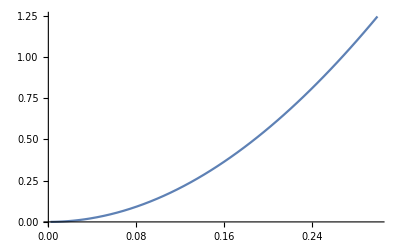

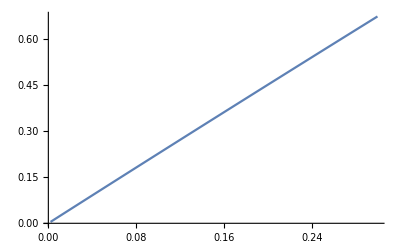

```mathematica
Plot[100*Cx/C0/.SolutionR1P2[[3,1]],{C0,0.002,0.3},PlotRange->All]
Plot[100*Cx/C0/.SolutionR1P1[[1,1]],{C0,0.002,0.3},PlotRange->All]
```